```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourrealnull"]]]==15&]}]
```

{-Graphics-29525,-Graphics-29527,-Graphics-29533,-Graphics-29551,-Graphics-29605,-Graphics-29767,-Graphics-30253,-Graphics-28764,-Graphics-31711,-Graphics-27246,-Graphics-36085,-Graphics-22708,-Graphics-49207,-Graphics-9490,-Graphics-364}

```mathematica
B2I[b_]:=If[b,1,0]
```

```mathematica
FiveVector[g_]:=Block[{result=Table[0,{k,10}], blocks,current},
blocks=Subsets[VertexList[g],{5}];
Table[
current=B2I[EdgeQ[g,b[[1]]<->b[[2]]]] +
B2I[EdgeQ[g,b[[1]]<->b[[3]]]] +
B2I[EdgeQ[g,b[[1]]<->b[[4]]]] +
B2I[EdgeQ[g,b[[1]]<->b[[5]]]] +
B2I[EdgeQ[g,b[[2]]<->b[[3]]]] +
B2I[EdgeQ[g,b[[2]]<->b[[4]]]] +
B2I[EdgeQ[g,b[[2]]<->b[[5]]]] +
B2I[EdgeQ[g,b[[3]]<->b[[4]]]] +
B2I[EdgeQ[g,b[[3]]<->b[[5]]]] +
B2I[EdgeQ[g,b[[4]]<->b[[5]]]] ;
result[[current+1]]=result[[current+1]]+1;
,{b,blocks}];
Reverse[result]
]
```

```mathematica
ThreeVector[g_]:=Block[{result=Table[0,{k,4}], blocks,current},
blocks=Subsets[VertexList[g],{3}];
Table[
current=B2I[EdgeQ[g,b[[1]]<->b[[2]]]] +
B2I[EdgeQ[g,b[[1]]<->b[[3]]]] +
B2I[EdgeQ[g,b[[2]]<->b[[3]]]]  ;
result[[current+1]]=result[[current+1]]+1;
,{b,blocks}];
Reverse[result]
]
```

```mathematica
Table[FiveVector[MinimalGraph[k]]//Total,{k,4,10}]
```

{1,6,21,56,126,252,462}

```mathematica
Table[ThreeVector[MinimalGraph[k]]//Total,{k,4,10}]
```

{10,20,35,56,84,120,165}

```mathematica
Total[{10,20,35,56,84,120,165}]
```

490

```mathematica
Table[Binomial[k,3],{k,1,20}]
```

{0,0,1,4,10,20,35,56,84,120,165,220,286,364,455,560,680,816,969,1140}

```mathematica
Table[FiveVector[JacobsThalGraph[k]]//Total,{k,4,10}]
```

{56,126,252,462,792,1287,2002}

```mathematica
Table[FiveVector[MinimalGraph2[k]]//Total,{k,4,10}]
```

{1,6,21,56,126,252,462}

```mathematica
Table[FiveVector[Graph[plantri[[k]]]]//Total,{k,4,10}]
```

{4368,4368,4368,6188,6188,6188,6188}

```mathematica
Table[Binomial[n,5],{n,5,20}]
```

{1,6,21,56,126,252,462,792,1287,2002,3003,4368,6188,8568,11628,15504}

```mathematica
FiveVector[EdgeDelete[CompleteGraph[5],1<->2]]
```

{1,0,0,0,0,0,0,0,0,0}

```mathematica
Table[FiveVector[g],{g, CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},3]}]
```

{{3,0,3,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{3,0,3,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{3,0,3,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{3,0,3,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0},{2,2,2,0,0,0,0,0,0,0}}

```mathematica
TableForm[Table[With[{v=ThreeVector[MinimalGraph2[k]]},Append[v,Style[Total[v],Red]]],{k,4,20}]]
```

7 | 3 | 0 | 0 | 10
10 | 8 | 2 | 0 | 20
13 | 15 | 6 | 1 | 35
16 | 22 | 16 | 2 | 56
19 | 28 | 34 | 3 | 84
22 | 33 | 60 | 5 | 120
25 | 47 | 74 | 19 | 165
28 | 55 | 106 | 31 | 220
31 | 60 | 150 | 45 | 286
34 | 57 | 216 | 57 | 364
37 | 80 | 236 | 102 | 455
40 | 84 | 300 | 136 | 560
43 | 103 | 340 | 194 | 680
46 | 99 | 432 | 239 | 816
49 | 103 | 514 | 303 | 969
52 | 123 | 570 | 395 | 1140
55 | 115 | 688 | 472 | 1330

```mathematica
TableForm[Table[With[{v=FiveVector[MinimalGraph2[k]]},Append[v,Style[Total[v],Red]]],{k,4,20}]]
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6
3 | 6 | 5 | 6 | 0 | 1 | 0 | 0 | 0 | 0 | 21
4 | 8 | 16 | 15 | 7 | 5 | 1 | 0 | 0 | 0 | 56
5 | 14 | 25 | 34 | 22 | 13 | 11 | 2 | 0 | 0 | 126
6 | 30 | 30 | 60 | 60 | 14 | 24 | 24 | 4 | 0 | 252
7 | 18 | 57 | 104 | 85 | 83 | 69 | 35 | 4 | 0 | 462
8 | 22 | 52 | 121 | 195 | 179 | 153 | 50 | 12 | 0 | 792
9 | 22 | 85 | 199 | 219 | 290 | 259 | 167 | 33 | 4 | 1287
10 | 34 | 85 | 207 | 378 | 469 | 450 | 254 | 97 | 18 | 2002
11 | 28 | 97 | 276 | 436 | 683 | 784 | 544 | 144 | 0 | 3003
12 | 50 | 132 | 389 | 642 | 833 | 982 | 775 | 484 | 69 | 4368
13 | 48 | 152 | 449 | 786 | 1209 | 1429 | 1230 | 703 | 169 | 6188
14 | 32 | 151 | 475 | 897 | 1527 | 2126 | 2336 | 948 | 62 | 8568
15 | 40 | 128 | 387 | 896 | 2316 | 3289 | 3024 | 1348 | 185 | 11628
16 | 46 | 177 | 532 | 1240 | 2597 | 3922 | 4147 | 2473 | 354 | 15504
17 | 36 | 133 | 450 | 1094 | 3195 | 5585 | 6640 | 2876 | 323 | 20349

```mathematica
CompFromPart3[count_,part_]:=Block[{result={}, g=CompleteGraph[count],current=0,vertices},
vertices=VertexList[g];
Table[
result=Append[result,EdgeList[VertexDelete[g,Take[vertices,p-Length[vertices]]]]];
g=VertexDelete[g,Take[vertices,p]];
vertices=Take[vertices,p-Length[vertices]];
,
{p,part}
];
result
]
```

```mathematica
ListSols3[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{4}]], comp,g},
Table[
comp=Flatten[CompFromPart3[count,part]];
g=EdgeDelete[CompleteGraph[count],comp];
g
,
{part, parts}
]
]
```

```mathematica
Table[MatrixForm[Map[{EdgeCount[#],3*VertexCount[#]-6,FiveVector[#]}&,ListSols3[k]]],{k,5,8}]
```

{(9 | 9 | {1,0,0,0,0,0,0,0,0,0}),(12 | 12 | {3,0,3,0,0,0,0,0,0,0}
13 | 12 | {4,2,0,0,0,0,0,0,0,0}),(15 | 15 | {6,0,12,0,0,3,0,0,0,0}
17 | 15 | {9,6,5,1,0,0,0,0,0,0}
18 | 15 | {12,9,0,0,0,0,0,0,0,0}),(18 | 18 | {10,0,30,0,0,15,0,0,0,1}
21 | 18 | {16,12,20,4,0,4,0,0,0,0}
22 | 18 | {18,18,14,6,0,0,0,0,0,0}
23 | 18 | {24,22,8,2,0,0,0,0,0,0}
24 | 18 | {32,24,0,0,0,0,0,0,0,0})}

```mathematica
Length[allGraphs6]
```

53071

```mathematica
goodSix=Table[allGraphs6[m,"graph"],{m,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&ChromaticPolynomial[allGraphs6[#,"graph"],4]>0&]}];
```

```mathematica
VectorComp[v1_,v2_]:=Block[{i, result={}},
For[i=1,i≤Length[v1],i++,
If[v1[[i]]<v2[[i]],
result=False;
Break[];
,
If[v1[[i]]>v2[[i]],
result=True;
Break[];
]
];
];
If[ToString[result]==ToString[{}],False,result]
]
```

```mathematica
StirlingS2[6,2]
```

31

```mathematica
Subsets[Range[6],{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

```mathematica
Binomial[6,5]
```

6

```mathematica
FiveVector[allGraphs6[0,"graph"]]
```

6

{0,0,0,0,0,0,0,0,0,6}

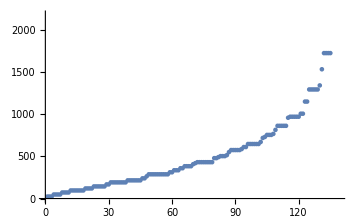

```mathematica
ListPlot[Map[#[[1,2]]&,Sort[Map[{FiveVector[#],ChromaticPolynomial[#,4]}&,goodSix]//Tally,#1[[1,2]]<#2[[1,2]]&]]]
```

```mathematica
Solve[4x+2y==1&&2x+2y+2z==1&&3x+3z==1,{x,y,z}]
```

{{x→1/6,y→1/6,z→1/6}}

```mathematica
TableForm[Sort[Map[{ThreeVector[#],ChromaticPolynomial[#,2]}&,goodSix]//Tally,VectorComp[#1[[1,1]],#2[[1,1]]]&],TableDepth->1]
```

{{{12,8,0,0},0},45}
{{{10,9,0,1},0},20}
{{{10,8,2,0},0},180}
{{{9,10,1,0},0},180}
{{{8,12,0,0},0},15}
{{{8,9,2,1},0},180}
{{{8,8,4,0},0},405}
{{{7,10,3,0},0},420}
{{{7,7,5,1},0},180}
{{{7,6,7,0},0},120}
{{{7,3,9,1},0},60}
{{{6,13,0,1},0},60}
{{{6,12,2,0},0},270}
{{{6,10,2,2},0},90}
{{{6,9,4,1},0},360}
{{{6,8,6,0},0},450}
{{{5,11,3,1},0},360}
{{{5,10,5,0},0},792}
{{{5,8,5,2},0},360}
{{{5,7,7,1},0},360}
{{{5,6,9,0},0},240}
{{{5,4,9,2},0},180}
{{{4,13,2,1},0},180}
{{{4,12,4,0},0},405}
{{{4,12,0,4},0},15}
{{{4,10,4,2},0},450}
{{{4,9,6,1},0},840}
{{{4,8,8,0},0},540}
{{{4,7,6,3},0},60}
{{{4,6,8,2},0},270}
{{{4,4,12,0},0},120}
{{{4,3,10,3},0},120}
{{{4,0,16,0},0},15}
{{{4,0,12,4},0},15}
{{{3,15,1,1},0},60}
{{{3,11,5,1},0},900}
{{{3,10,7,0},0},720}
{{{3,10,3,4},0},120}
{{{3,9,5,3},0},360}
{{{3,8,7,2},0},1080}
{{{3,7,9,1},0},720}
{{{3,6,11,0},0},180}
{{{3,6,7,4},0},60}
{{{3,5,9,3},0},360}
{{{2,14,2,2},0},90}
{{{2,13,4,1},0},360}
{{{2,12,6,0},0},60}
{{{2,10,6,2},0},900}
{{{2,9,8,1},0},1260}
{{{2,9,4,5},0},180}
{{{2,8,10,0},0},360}
{{{2,8,6,4},0},270}
{{{2,7,8,3},0},1080}
{{{2,6,10,2},0},900}
{{{2,5,12,1},0},360}
{{{2,5,8,5},0},360}
{{{2,4,14,0},0},90}
{{{2,4,10,4},0},450}
{{{2,2,14,2},0},90}
{{{2,2,10,6},0},90}
{{{2,0,18,0},0},10}
{{{1,12,5,2},0},360}
{{{1,11,7,1},0},360}
{{{1,9,7,3},0},720}
{{{1,9,3,7},0},60}
{{{1,8,9,2},0},1260}
{{{1,7,11,1},0},360}
{{{1,7,7,5},0},360}
{{{1,6,9,4},0},840}
{{{1,5,11,3},0},900}
{{{1,5,7,7},0},180}
{{{1,4,13,2},0},360}
{{{1,4,9,6},0},360}
{{{1,3,11,5},0},360}
{{{1,2,13,4},0},180}
{{{1,2,9,8},0},180}
{{{1,1,15,3},0},60}
{{{1,0,13,6},0},60}
{{{1,0,9,10},0},20}
{{{0,18,0,2},2},10}
{{{0,16,0,4},2},15}
{{{0,14,4,2},2},90}
{{{0,12,4,4},2},120}
{{{0,11,6,3},2},180}
{{{0,10,8,2},0},180}
{{{0,10,8,2},2},180}
{{{0,10,0,10},2},6}
{{{0,9,6,5},4},60}
{{{0,9,6,5},2},180}
{{{0,8,8,4},2},540}
{{{0,7,10,3},0},360}
{{{0,7,10,3},2},360}
{{{0,7,6,7},2},120}
{{{0,6,12,2},2},60}
{{{0,6,8,6},4},360}
{{{0,6,8,6},2},90}
{{{0,6,4,10},4},30}
{{{0,5,10,5},0},72}
{{{0,5,10,5},2},720}
{{{0,4,12,4},2},360}
{{{0,4,12,4},4},45}
{{{0,4,8,8},8},45}
{{{0,4,8,8},4},360}
{{{0,3,10,7},4},420}
{{{0,3,6,11},8},60}
{{{0,2,12,6},4},270}
{{{0,2,8,10},8},180}
{{{0,1,10,9},8},180}
{{{0,1,6,13},16},60}
{{{0,0,12,8},8},15}
{{{0,0,8,12},16},45}
{{{0,0,4,16},32},15}
{{{0,0,0,20},64},1}

```mathematica
Take[goodSix,2]
```

```mathematica
FiveVector[allGraphs6[0,"graph"]]
```

{0,0,0,0,0,0,0,0,0,6}

```mathematica
ChromaticPolynomial[-Graphics-,5]
```

10000

```mathematica
Table[GraphComplement[allGraphs6[k,"graph"],VertexLabels->"Name",ImageSize->70],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
ChromaticPolynomial[g,4]==24&&FiveVector[g]=={4,2,0,0,0,0,0,0,0,0}
]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ChromaticPolynomial[-Graphics-,5]
```

```mathematica
Table[GraphComplement[allGraphs6[k,"graph"],VertexLabels->"Name",ImageSize->70],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
ChromaticPolynomial[g,4]==24&&FiveVector[g]=={3,0,3,0,0,0,0,0,0,0}
]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ChromaticPolynomial[-Graphics-,5]
```

8000

```mathematica
Table[GraphComplement[allGraphs6[k,"graph"],VertexLabels->"Name",ImageSize->70],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
ChromaticPolynomial[g,4]==24&&FiveVector[g]=={2,2,2,0,0,0,0,0,0,0}
]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphComplement[allGraphs6[k,"graph"],VertexLabels->"Name",ImageSize->70],{k,Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},
ChromaticPolynomial[g,4]==48&&FiveVector[g]=={1,4,1,0,0,0,0,0,0,0}
]&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TableForm[Sort[Map[{FiveVector[#],ChromaticPolynomial[#,4]}&,goodSix]//Tally,VectorComp[#1[[1,1]],#2[[1,1]]]&],TableDepth->1]
```

{{{4,2,0,0,0,0,0,0,0,0},24},45}
{{{2,2,2,0,0,0,0,0,0,0},24},180}
{{{3,0,3,0,0,0,0,0,0,0},24},20}
{{{1,4,1,0,0,0,0,0,0,0},48},180}
{{{1,1,3,1,0,0,0,0,0,0},48},360}
{{{0,4,0,2,0,0,0,0,0,0},48},45}
{{{1,2,1,2,0,0,0,0,0,0},48},180}
{{{1,0,5,0,0,0,0,0,0,0},72},60}
{{{1,0,1,4,0,0,0,0,0,0},72},120}
{{{0,3,2,1,0,0,0,0,0,0},72},360}
{{{1,0,2,2,1,0,0,0,0,0},72},180}
{{{0,6,0,0,0,0,0,0,0,0},96},15}
{{{0,2,4,0,0,0,0,0,0,0},96},90}
{{{0,2,0,4,0,0,0,0,0,0},96},90}
{{{1,0,0,2,3,0,0,0,0,0},96},60}
{{{0,1,3,1,1,0,0,0,0,0},96},360}
{{{0,2,1,2,1,0,0,0,0,0},96},360}
{{{0,2,2,0,2,0,0,0,0,0},96},90}
{{{0,2,4,0,0,0,0,0,0,0},120},180}
{{{0,1,2,3,0,0,0,0,0,0},120},360}
{{{0,0,5,0,1,0,0,0,0,0},120},72}
{{{0,3,2,1,0,0,0,0,0,0},120},60}
{{{0,1,2,3,0,0,0,0,0,0},144},360}
{{{0,1,0,3,2,0,0,0,0,0},144},180}
{{{0,1,1,1,3,0,0,0,0,0},144},360}
{{{0,0,2,3,0,1,0,0,0,0},144},60}
{{{0,1,3,1,1,0,0,0,0,0},144},360}
{{{0,1,1,2,1,1,0,0,0,0},144},360}
{{{0,0,4,2,0,0,0,0,0,0},168},360}
{{{0,0,2,2,2,0,0,0,0,0},168},180}
{{{0,0,4,2,0,0,0,0,0,0},192},45}
{{{0,0,2,2,2,0,0,0,0,0},192},360}
{{{0,1,2,3,0,0,0,0,0,0},192},180}
{{{0,0,3,0,3,0,0,0,0,0},192},120}
{{{0,1,0,1,2,2,0,0,0,0},192},180}
{{{0,0,2,3,0,1,0,0,0,0},192},360}
{{{0,0,3,1,1,1,0,0,0,0},192},360}
{{{0,0,4,0,0,2,0,0,0,0},192},15}
{{{0,0,1,4,1,0,0,0,0,0},216},360}
{{{0,0,1,1,3,1,0,0,0,0},216},120}
{{{0,1,0,3,2,0,0,0,0,0},216},360}
{{{0,0,2,0,2,2,0,0,0,0},216},180}
{{{0,0,4,2,0,0,0,0,0,0},216},60}
{{{0,1,0,4,0,1,0,0,0,0},216},90}
{{{0,0,2,0,3,0,1,0,0,0},216},60}
{{{0,0,1,4,1,0,0,0,0,0},240},360}
{{{0,0,2,2,2,0,0,0,0,0},240},900}
{{{0,0,0,6,0,0,0,0,0,0},264},60}
{{{0,0,0,2,0,4,0,0,0,0},288},15}
{{{0,0,0,3,2,1,0,0,0,0},288},180}
{{{0,0,1,4,1,0,0,0,0,0},288},360}
{{{0,0,1,1,3,1,0,0,0,0},288},720}
{{{0,1,0,0,4,1,0,0,0,0},288},90}
{{{0,0,1,1,0,3,1,0,0,0},288},120}
{{{0,0,1,2,1,2,0,0,0,0},288},900}
{{{0,0,0,4,1,0,1,0,0,0},288},180}
{{{0,0,1,2,2,0,1,0,0,0},288},360}
{{{0,0,1,3,0,1,1,0,0,0},288},120}
{{{0,0,0,2,4,0,0,0,0,0},312},180}
{{{0,0,2,2,2,0,0,0,0,0},312},90}
{{{0,0,0,2,4,0,0,0,0,0},336},180}
{{{0,0,0,3,2,1,0,0,0,0},336},1080}
{{{0,0,0,4,0,2,0,0,0,0},336},180}
{{{0,0,1,0,5,0,0,0,0,0},360},180}
{{{0,0,1,1,3,1,0,0,0,0},360},720}
{{{0,0,0,2,4,0,0,0,0,0},384},360}
{{{0,0,0,2,0,0,4,0,0,0},384},15}
{{{0,0,1,0,2,2,1,0,0,0},384},360}
{{{0,0,1,0,3,0,2,0,0,0},384},60}
{{{0,0,0,3,2,1,0,0,0,0},408},360}
{{{0,0,0,6,0,0,0,0,0,0},420},10}
{{{0,0,0,0,4,2,0,0,0,0},432},90}
{{{0,0,0,1,2,3,0,0,0,0},432},360}
{{{0,0,0,2,0,4,0,0,0,0},432},180}
{{{0,0,0,1,3,1,1,0,0,0},432},720}
{{{0,0,0,2,1,2,1,0,0,0},432},900}
{{{0,0,0,2,2,0,2,0,0,0},432},180}
{{{0,0,0,1,4,0,0,1,0,0},432},90}
{{{0,0,0,2,2,1,0,1,0,0},432},180}
{{{0,0,0,0,4,2,0,0,0,0},480},360}
{{{0,0,1,0,1,4,0,0,0,0},480},180}
{{{0,0,0,2,4,0,0,0,0,0},492},90}
{{{0,0,0,1,2,3,0,0,0,0},504},1080}
{{{0,0,0,0,5,0,1,0,0,0},504},180}
{{{0,0,0,1,3,1,1,0,0,0},504},720}
{{{0,0,0,4,0,2,0,0,0,0},516},15}
{{{0,0,0,0,4,2,0,0,0,0},552},180}
{{{0,0,0,0,0,6,0,0,0,0},576},10}
{{{0,0,0,0,2,2,2,0,0,0},576},90}
{{{0,0,0,1,1,1,3,0,0,0},576},360}
{{{0,0,0,1,0,4,0,1,0,0},576},90}
{{{0,0,0,1,1,2,1,1,0,0},576},360}
{{{0,0,0,0,4,2,0,0,0,0},588},180}
{{{0,0,0,1,2,3,0,0,0,0},612},180}
{{{0,0,0,1,3,1,1,0,0,0},612},120}
{{{0,0,0,0,1,4,1,0,0,0},648},360}
{{{0,0,0,0,2,2,2,0,0,0},648},900}
{{{0,0,0,0,3,0,3,0,0,0},648},120}
{{{0,0,0,0,2,3,0,1,0,0},648},360}
{{{0,0,0,0,3,1,1,1,0,0},648},360}
{{{0,0,0,0,3,2,0,0,1,0},648},60}
{{{0,0,0,1,0,3,2,0,0,0},672},360}
{{{0,0,0,0,1,4,1,0,0,0},720},360}
{{{0,0,0,0,0,6,0,0,0,0},732},60}
{{{0,0,0,0,1,4,1,0,0,0},756},360}
{{{0,0,0,0,2,2,2,0,0,0},756},540}
{{{0,0,0,0,2,3,0,1,0,0},756},180}
{{{0,0,0,0,2,0,2,2,0,0},768},90}
{{{0,0,0,1,0,3,2,0,0,0},816},60}
{{{0,0,0,0,0,2,4,0,0,0},864},60}
{{{0,0,0,0,0,3,2,1,0,0},864},180}
{{{0,0,0,0,1,1,3,1,0,0},864},360}
{{{0,0,0,0,1,2,1,2,0,0},864},360}
{{{0,0,0,0,1,2,2,0,1,0},864},180}
{{{0,0,0,0,1,0,5,0,0,0},960},72}
{{{0,0,0,0,0,2,4,0,0,0},972},360}
{{{0,0,0,0,0,3,2,1,0,0},972},720}
{{{0,0,0,0,0,4,0,2,0,0},972},90}
{{{0,0,0,0,0,4,1,0,1,0},972},120}
{{{0,0,0,0,0,5,0,0,0,1},972},6}
{{{0,0,0,0,0,2,4,0,0,0},1008},45}
{{{0,0,0,0,1,1,3,1,0,0},1008},360}
{{{0,0,0,0,0,1,2,3,0,0},1152},60}
{{{0,0,0,0,0,2,1,2,1,0},1152},180}
{{{0,0,0,0,0,0,4,2,0,0},1296},270}
{{{0,0,0,0,0,1,2,3,0,0},1296},360}
{{{0,0,0,0,0,0,5,0,1,0},1296},60}
{{{0,0,0,0,0,1,3,1,1,0},1296},360}
{{{0,0,0,0,0,1,4,0,0,1},1296},30}
{{{0,0,0,0,0,2,0,4,0,0},1344},45}
{{{0,0,0,0,0,0,3,0,3,0},1536},20}
{{{0,0,0,0,0,0,0,6,0,0},1728},15}
{{{0,0,0,0,0,0,1,4,1,0},1728},180}
{{{0,0,0,0,0,0,2,2,2,0},1728},180}
{{{0,0,0,0,0,0,2,3,0,1},1728},60}
{{{0,0,0,0,0,0,0,2,4,0},2304},45}
{{{0,0,0,0,0,0,0,3,2,1},2304},60}
{{{0,0,0,0,0,0,0,0,4,2},3072},15}
{{{0,0,0,0,0,0,0,0,0,6},4096},1}

```mathematica
StirlingS2[6,5]
```

15

```mathematica
Table[MatrixForm[Map[{EdgeCount[#],3*VertexCount[#]-6,MaximalPlanarQ[#]}&,ListSols3[k]]],{k,5,8}]
```

{(9 | 9 | True),(12 | 12 | False
13 | 12 | False),(15 | 15 | False
17 | 15 | False
18 | 15 | False),(18 | 18 | False
21 | 18 | False
22 | 18 | False
23 | 18 | False
24 | 18 | False)}